#### Assignment 1: Position is the integral of velocity

Define a function of time: v(t) = v0 - g t, where v0 is a variable defined to be 5 and g is a variable defined to be 9.8. Define x(t) to be the integral of that function. Plot both v(t) and x(t) on same graph with different colors, for t = 0 to 2.

5

9.8

5-9.8 t

5 t-4.9 t^2

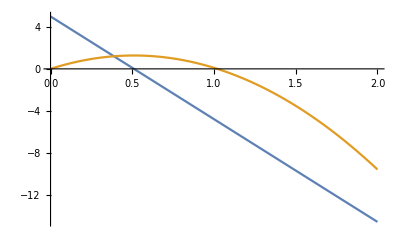

```mathematica
v0 =5
g =9.8
v[t_]=v0-g*t
x[t_]=Integrate[v[t],t]
Plot[{v[t],x[t]},{t,0,2}]
```

#### Assignment 2: Solving an equation, numerically

For what value of x (in radians) does cos(x) = x?  
(a) Start by plotting cos(x) and x on the same graph. You can get an approximate answer by looking at where the two curves intersect: that’s where cos(x) equals x. 
(b) Then use FindRoot to get a precise answer.

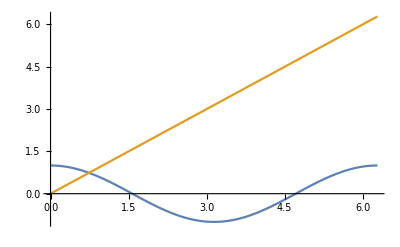

```mathematica
fq[
Plot[{Cos[x],x},{x,0,2Pi}]
```

```mathematica
FindRoot[Cos[x]==x,{x,1}]
```

{x→0.739085}

#### Assignment 3: Diffraction from a slit

In Physics 232 you hopefully learned that the diffraction pattern produced by a single slit of non-negligible width is given by:  I(x) = I_0  ((sin(πxa/λL))/(πxa/λL))^2, where a is the slit width, L is the distance to the screen where the pattern is being observed, and x is the position on the screen.  (Disclaimer: this involves a small angle approximation.) Sometimes that equation is written in terms of the "sinc" function, where sinc(x)=(sin(x))/x. (Incidentally, Sinc is a pre-defined function in Mathematica, just like Sin itself.) In the equation, I_0 is the intensity at x = 0, i.e. the mid-point of the diffraction pattern; let's just define that as 1 for simplicity.
(a) Make a plot of this function for 3 or 4 maxima around each side of the central maximum, for a 100 micron slit, a 633 nm laser, and a distance to screen = 10 m. Make two plots, actually: one with the default y-axis (meaning intensity)  range, and a second one where you use a PlotRange option to “zoom out” and fully see the central peak.
(b) Determine the position of the first maximum to the right of the central maximum. Side note: In Physics 232 you learned a simple formula for the minima, but there is no similar simple formula for the maxima. They are only approximately located equidistant between the minima.

1/10000

633/1000000000

10

1

(400689 Sin[(10000 π x)/633]^2)/(100000000 π^2 x^2)

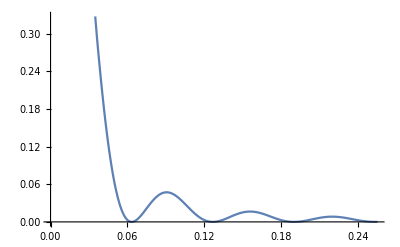

```mathematica
a=100*10^-6 (* slit width converted to meters*)
lambda = 633*10^-9 (* wavelength of laser light converted to meters*)
capL = 10 (*distance from slit to screen in meters*)
capInaught = 1 (*intensity at midpoint of diffraction pattern*)
i[x_]=capInaught*((Sin[(Pi*x*a)/(lambda*capL)]/((Pi*x*a)/(lambda*capL))))^2
Plot[i[x],{x,0,0.255}]
```

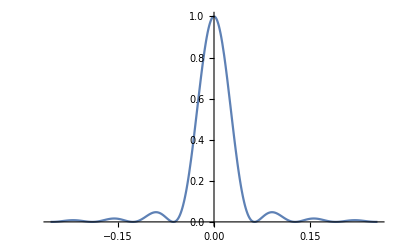

```mathematica
Plot[i[x],{x,-0.255,0.255},PlotRange->All]
```

#### Assignment 4: Two summations

(a) Calculate the value of  ∑_(n=1)^∞ 1/n^6, in both symbolic and numerical form. 
(b) Calculate the value of 1 - 1/2 + 1/3 - 1/4 + 1/5 - 1/6 + ...

```mathematica
Sum[1/(n^6),{n,1,Infinity}]
```

π^6/945

```mathematica
N[%]
```

1.01734

```mathematica
Sum[((-1)^n)/n!,{n,0,Infinity}]
```

1/ⅇ

#### Assignment 5: The plot thickens

Make a plot of x^4 + 2 x^3 +3 x^2+ 4 x+5, from x = -3 to x = 3. Experiment with different plot styles as options, such as PlotStyle→Thick,  or PlotStyle→Red (or Blue, or Green, or Magenta, etc.), or PlotStyle→Dashed  (or Dotted, or DotDashed), or PlotStyle→Opacity[0.5] (or Opacity[0.1], or Opacity[0.8], etc.). After you have experimented a bit with these options, choose your favorite plot styles and combine them together via a list enclosed in braces: PlotStyle→{option1, option2, option3, etc.}.

5+4 x+3 x^2+2 x^3+x^4

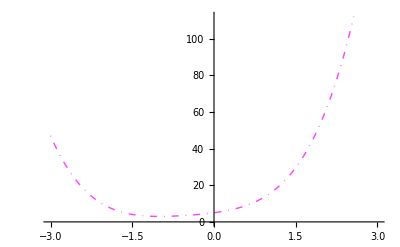

```mathematica
q[x] = x^4+2x^3+3x^2+4x+5
Plot[q[x],{x,-3,3},PlotStyle->{DotDashed,Opacity[0.75],Magenta,Thick}]
```

#### Assignment 6: Polynomial roots

As you should have just seen from the plot, the polynomial x^4 + 2 x^3 + 3 x^2 + 4 x + 5 has no real roots. (It doesn' t cross zero anywhere.) It does, however, have four complex roots. What are they? Find them in decimal form.

```mathematica
FindRoot[x^4+2x^3+3x^2+4x+5==0,{x,I}]
FindRoot[x^4+2x^3+3x^2+4x+5==0,{x,-1*I}]
FindRoot[x^4+2x^3+3x^2+4x+5==0,{x,(1/2)*I}]
FindRoot[x^4+2x^3+3x^2+4x+5==0,{x,(-1/2)*I}]
```

{x→0.287815+1.41609 ⅈ}

{x→0.287815-1.41609 ⅈ}

{x→-1.28782+0.857897 ⅈ}

{x→-1.28782-0.857897 ⅈ}

{x→0.287815-1.41609 ⅈ}

```mathematica
NSolve[Reduce[q[x]*I==0],x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→q^(-1)[0.]}}

```mathematica
Reduce[%]
```

Reduce::naqs: {x→q^(-1)[0.]} is not a quantified system of equations and inequalities.

Reduce[{{x→q^(-1)[0.]}}]

#### Assignment 7: Taylor’s series of e^x

The Taylor’s series of e^x evaluated at x = 1 is 1 + 1 + 1/2 + 1/3! + 1/4!  + ... .  Show that this series gets closer and closer to the true value of e  (=e^1) as you include more and more terms. Try 5 terms (as shown), 10 terms, and 100 terms; give your results to 50 decimal places. Also display e to 50 decimal places for comparison.

```mathematica
N[E,50]
N[1+1+(1/2)+(1/(3!))+(1/(4!)), 50]
N[Sum[1/(n!),{n,0,5}],50]
N[Sum[1/(n!),{n,0,10}],50]
N[Sum[1/(n!),{n,0,100}],50]
N[E,50]
```

2.7182818284590452353602874713526624977572470937

2.7083333333333333333333333333333333333333333333333

2.7166666666666666666666666666666666666666666666667

2.7182818011463844797178130511463844797178130511464

2.7182818284590452353602874713526624977572470937

2.7182818284590452353602874713526624977572470937

#### Assignment 8: A basic derivative

Define the function f8(x) = (sin^2(x))/(1+cos(x)). Take its derivative, and simplify the result.

```mathematica
f8[x_]=Sin[x]^2/(1+Cos[x])
f8'[x]
Simplify[f8'[x]]
```

Sin[x]^2/(1+Cos[x])

(2 Cos[x] Sin[x])/(1+Cos[x])+Sin[x]^3/(1+Cos[x])^2

Sin[x]

#### Assignment 9: A basic integral

Determine  ∫e^-x sin(x)ⅆx, integrated from 0 to infinity.

```mathematica
f9[x_]=Sin[x]*E^(-x)
Integrate[f9[x],{x,0,Infinity}]
```

ⅇ^-x Sin[x]

1/2

Let’s start with a simple complex number in z = x + iy format (rectangular format):

```mathematica
z=4+3I
```

It has real and imaginary parts:

```mathematica
Re[z]
Im[z]
```

And we can calculate its complex conjugate:

```mathematica
Conjugate[z]
```

When plotted on the complex plane (x-axis is the real axis, y-axis is the imaginary axis), then the length (the absolute value, or magnitude of z) and angle of that line provides us with the parameters for representing z in polar format:

```mathematica
Abs[z]
Arg[z]
```

You can do many of these things quite simply using the “suggestions bar” that appears when you evaluate an input or click on an output box.  Try that by executing the input line below, and choose “convert to exponential” to convert the rectangular format of z to a polar format.  When you do this you’ll recognize in this format the absolute value and the angle that you calculated above.

```mathematica
z
```

This is essentially Euler’s equation: z = e^iθ = cos(θ) + i sin(θ) = x + iy. 
Now instead of working with an individual complex number, let’s think about a simple complex function written in polar format,  z = e^ix:

```mathematica
f[x_]= E^(I x)
```

The real part should be cos(x).  Let’s see:

```mathematica
Re[f[x]]
```

Well this is certainly true, but not particularly helpful.  The suggestions bar offers the suggestion “FullSimplify”.  Give that a try:

```mathematica
FullSimplify[Re[ⅇ^(ⅈ x)]]
```

Still no cosine function.  However, as you’ll see next, it seems Mathematica can still evauate Re(f(x)) at a point, and has no trouble plotting it as a function of x:

```mathematica
Re[f[Pi/4]]
Plot[Re[f[x]],{x,0,15}]
```

What’s happeining here?  The problem is that Mathematica doesn’t know in general whether x is real, imaginary or complex. When we ask it to evaluate f(x) for a real value of x, or plot f(x) over a range of real values then we’re making it explicit that we’re talking about real values of x.  But Mathematica can’t know if that is always the case.  This is a perfect example of a situation where we need to provide Mathematica with a little more information.   Let’s declare x to be a real number.  Here’s what that looks like:

```mathematica
$Assumptions=x∈Reals
```

```mathematica
Re[f[x]]
```

```mathematica
FullSimplify[Re[ⅇ^(ⅈ x)]]
```

The Assumptions statement says “x is an element of the set of real numbers”.  The symbol ∈, “is an element of,” is produced by typing the sequence Esc elem Esc.
The power of the FullSimplify command is that it takes any assumptions that have been made and applies them in making the simplification.

#### Assignment 10: A basic complex number calculation

(a) Calculate the magnitude and angle (in radians) of:  (4 + 5i) ÷ (6 - 7i).  Give your answers in decimal form to 8 sig figs.
(b) Show that the magnitude squared of the number is also the number times its complex conjugate

```mathematica
a10=(4+5I)/(6-7I)
```

-11/85+(58 ⅈ)/85

Plot::plld: Endpoints for Charting`Private`pvar$9152 in {Charting`Private`pvar$9152,0,0} must have distinct machine-precision numerical values.

General::stop: Further output of Plot::plld will be suppressed during this calculation.

Plot[a10,{x,0,ⅈ}]

```mathematica
re =Re[(a10)]
im =Im[a10]
mag =Sqrt[re^2+im^2](*calculates magnitude of a10*)
ang =N[ mag*Tan[im/re]]
```

-11/85

58/85

√(41/85)

1.10694

#### Assignment 11: Superposition of wavefunctions

Define two wavefunctions: ψ1 = e^(i k1 x) and ψ2 = e^(i k2x), where k1 = 1 and k2 = 2.  (If you want, you can get the Greek letter ψ by typing Esc psi Esc.  Or just call it psi!)  
(a) Plot the real parts of ψ1 and ψ2 on the same graph using different colors, over the x-range 0 to 15.  Then on a second graph and over the same range, plot the real part of the superposition ψ12 = ψ1 + ψ2.
(b) Define the (non-normalized) probability function prob1 to be the wavefunction ψ1 times its complex conjugate.  Do the same for prob2 and prob12.
(c) Show that even though the wavefunctions are complex, the probabilities are always real.  Hint: use $Assumptions and FullSimplify, or play around with the commands ExpToTrig or ComplexExpand (which makes its own assumptions) in combination with Simplify.
(b) Make a plot of the probabilities which demonstrates that prob12 ≠ prob1 + prob2.

```mathematica
(*setup*)
k1 = 1
k2 = 2
ψ1[x_]=E^(I*k1*x)
ψ2[x_]=E^(I*k2*x)
ψ12[x_]=ψ1[x]+ψ2[x]
```

1

2

ⅇ^(ⅈ x)

ⅇ^(2 ⅈ x)

ⅇ^(ⅈ x)+ⅇ^(2 ⅈ x)

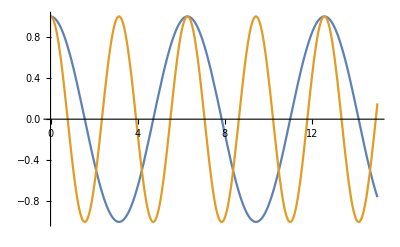

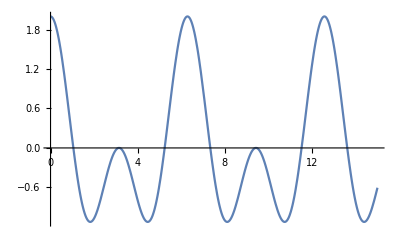

```mathematica
(*a*)
Plot[{Re[ψ1[x]],Re[ψ2[x]]},{x,0,15}]
Plot[Re[ψ12[x]],{x,0,15}]
```

```mathematica
(*b*)
prob1[x_]=ψ1[x]*Conjugate[ψ1[x]]
prob2[x_]=ψ2[x]*Conjugate[ψ2[x]]
prob12[x_]=ψ12[x]*Conjugate[ψ12[x]]
```

ⅇ^(ⅈ x-ⅈ Conjugate[x])

ⅇ^(2 ⅈ x-2 ⅈ Conjugate[x])

(ⅇ^(ⅈ x)+ⅇ^(2 ⅈ x)) (ⅇ^(-ⅈ Conjugate[x])+ⅇ^(-2 ⅈ Conjugate[x]))

```mathematica
(*c*)
ComplexExpand[ψ1[x]]
ComplexExpand[prob1[x]]
ComplexExpand[ψ2[x]]
ComplexExpand[prob2[x]]
ComplexExpand[ψ12[x]]
ComplexExpand[prob12[x]]
```

Cos[x]+ⅈ Sin[x]

1

Cos[2 x]+ⅈ Sin[2 x]

1

Cos[x]+Cos[2 x]+ⅈ (Sin[x]+Sin[2 x])

Cos[x]^2+2 Cos[x] Cos[2 x]+Cos[2 x]^2+Sin[x]^2+2 Sin[x] Sin[2 x]+Sin[2 x]^2

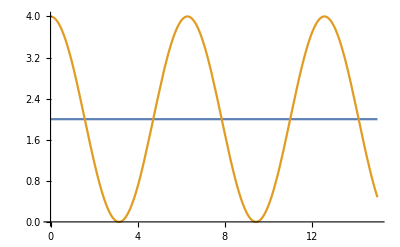

```mathematica
(*d*)
Plot[{prob1[x]+prob2[x],prob12[x]},{x,0,15}]
```

## What to turn in

When you are done, SAVE this entire file, with all your work.  Then SAVE it again under the new name “HW#2-yourname”, where yourname is of course, your name.  Delete all but the Assignments themselves (of which there are 11).  Make sure the entire worksheet runs correctly and that you haven’t deleted anything important!  Turn in this assignment worksheet, with all of its input and output code, through the link on our Moodle page.

Here’s what it should look like: